```mathematica
sumIntDigits[n_, b_]:=Total[IntegerDigits[n, b]]
```

```mathematica
sumIntDigits[17, 10]
```

8

```mathematica
sumIntDigits[10, 2]
```

2

```mathematica
expSumList[n_ ,b_, p_]:=Prepend[Accumulate[Exp[2.0*Pi*I*sumIntDigits[#, b]/p]&/@Range[n]], 0]
```

```mathematica
Range[4.23123]
```

{1,2,3,4}

```mathematica
expSumList[1000,10, 4];
```

```mathematica
expSumList[7, 2, 3]
```

{0,-0.5+0.866025 ⅈ,-1.+1.73205 ⅈ,-1.5+0.866025 ⅈ,-2.+1.73205 ⅈ,-2.5+0.866025 ⅈ,-3.+1.33227×10^-15 ⅈ,-2.+1.08734×10^-15 ⅈ}

```mathematica
visualizer[n_, b_, p_]:=ListLinePlot[ReIm /@ expSumList[n,b, p], PlotStyle->Thick]
```

```mathematica
chunkVisualizer[n1_, n2_, b_, p_, c_]:=ListLinePlot[ReIm /@ Take[expSumList[n2,b, p], {n1, n2+1}], PlotStyle->{Thick, c}]
```

```mathematica
pointVisualizer[n_, b_, p_]:=ListPlot[ReIm /@ expSumList[n,b, p], PlotStyle->{PointSize[Large], Red}]
```

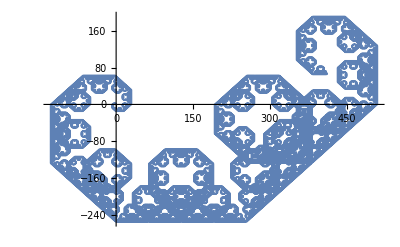

```mathematica
visualizer[100000, 2, 4]
```

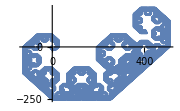

```mathematica
Show[%,ImageSize->Small]
```

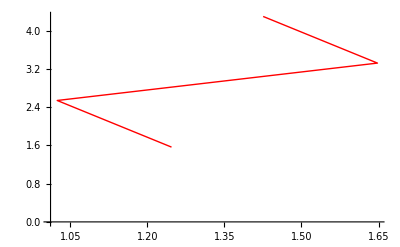

```mathematica
chunkVisualizer[3,5,2, 7, Red]
```

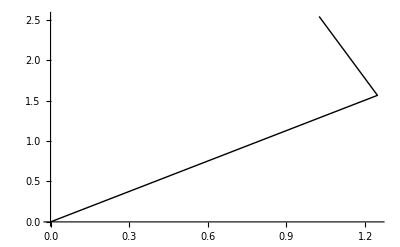

```mathematica
chunkVisualizer[1,3,2, 7, Black]
```

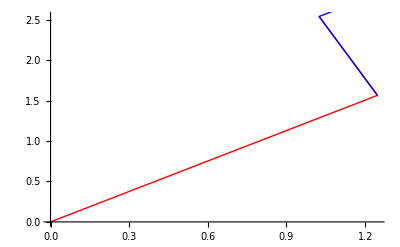

```mathematica
Show[chunkVisualizer[1,3,2, 7, Red], chunkVisualizer[3,5,2, 7, Blue]]
```

```mathematica
(* Table of some integer visualizations in base 10, varying by param p *)
```

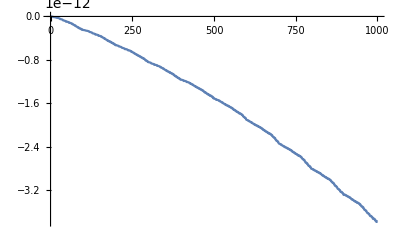
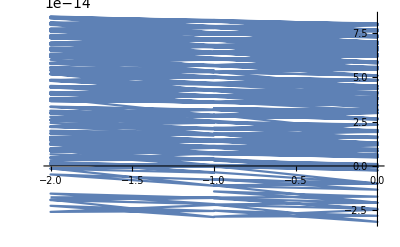
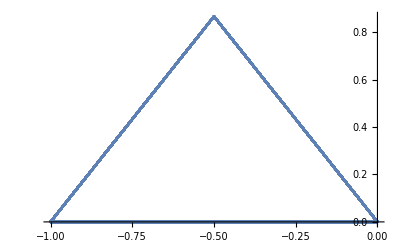
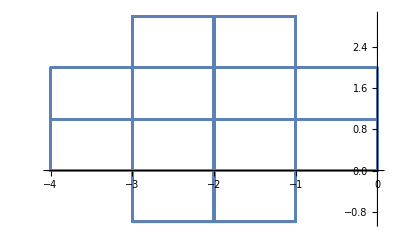
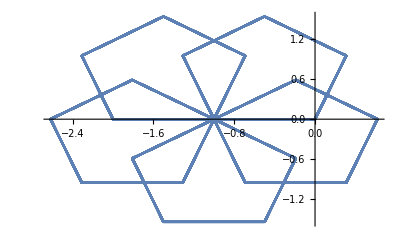
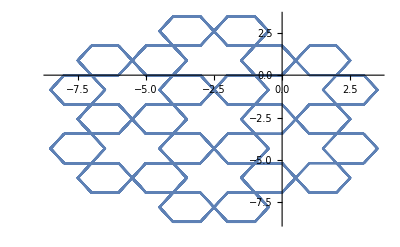
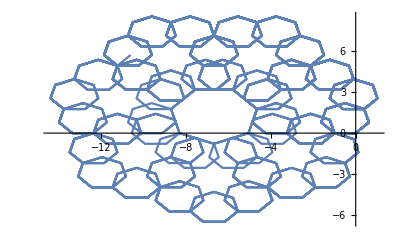
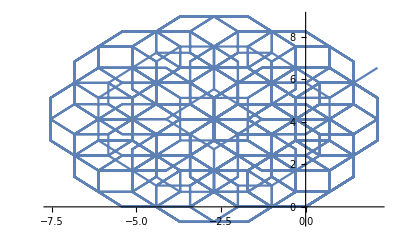
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
Table[{k,ListLinePlot[(ReIm /@ expSumList[1000, 10, k])]}, {k, Range[10]}]
```

```mathematica
(* Table of some integer visualizations in base 10, varying by param n *)
```

```mathematica
Manipulate[list = ReIm /@ expSumList[10000, 2, 4];
maxRange = Max[Abs[list]];
ListLinePlot[Take[list,t],PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}], {t, 1, 10000, 1}]
```

```mathematica
Manipulate[list = ReIm /@ expSumList[10000, 2, 1/Sqrt[3]];
partialList = Take[list, t];
maxRange = Max[Abs[partialList]]*1.1;
Graphics[Line[partialList], PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}, Axes->True], {t, 2, 10000, 10}]
```

```mathematica
(* Table of some integer visualizations varying in base *)
```

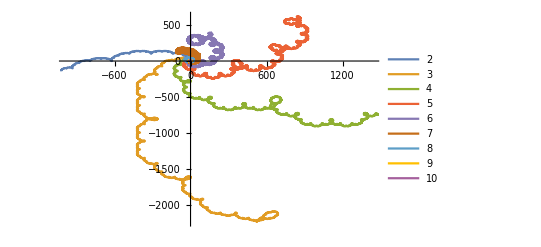

```mathematica
ListLinePlot[(ReIm /@ expSumList[10000, #, 10])& /@ Range[2,10], PlotLegends->Range[2,10]]
```

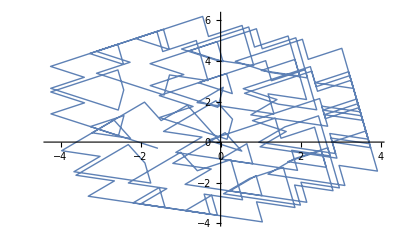

```mathematica
visualizer[250, 2, Pi]
```

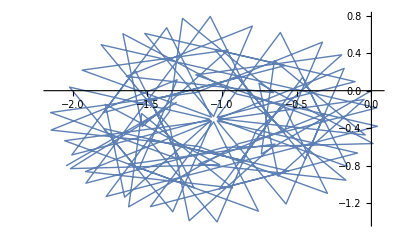

```mathematica
visualizer[100, 10, GoldenRatio]
```

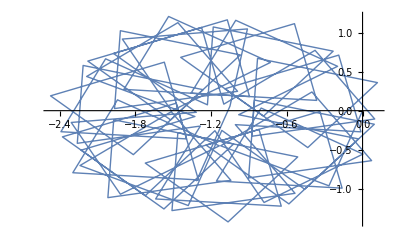

```mathematica
visualizer[100, 10, Sqrt[2]]
```

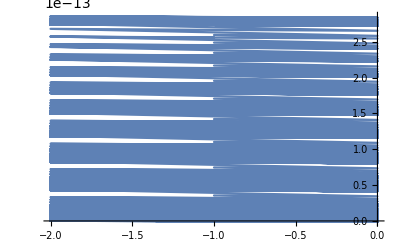
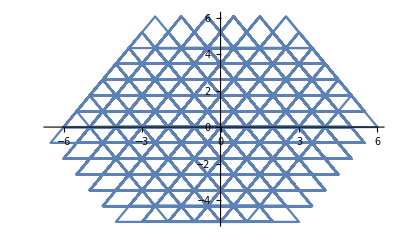
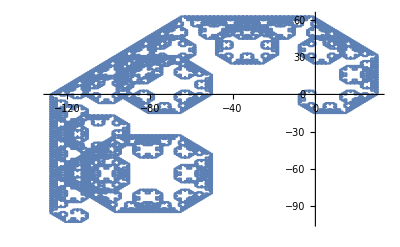
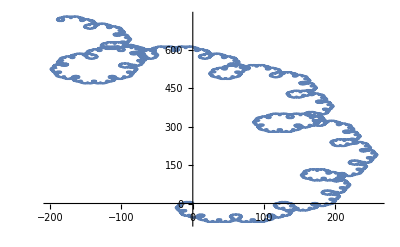
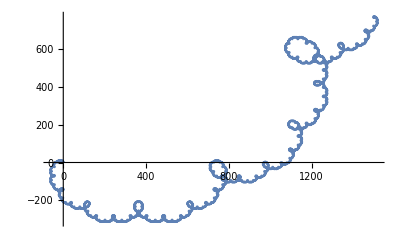
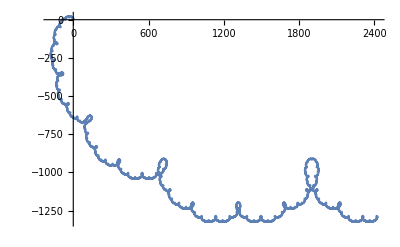
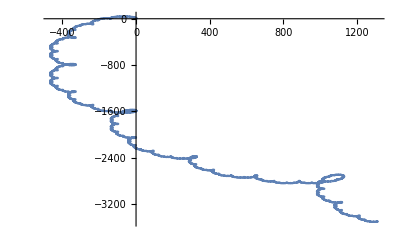
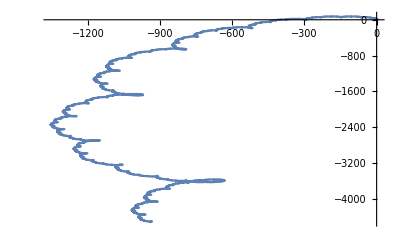
{{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
(*Table of sumWalks for base 2*)
Sort[Table[{x, ListLinePlot[ReIm /@ expSumList[10000, 2, x]]}, {x, Range[2,10]}]]
```

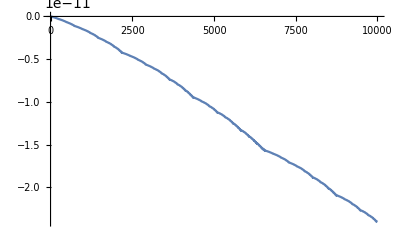
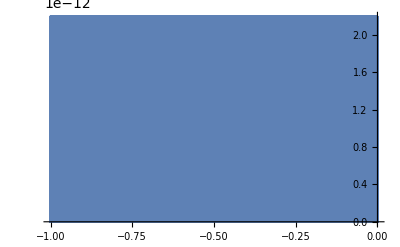
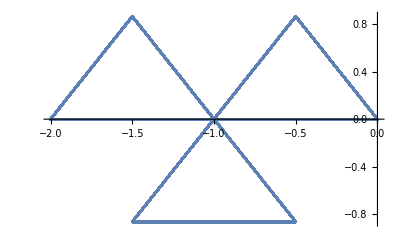
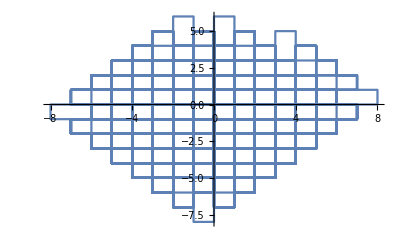
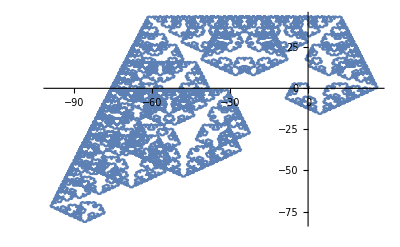
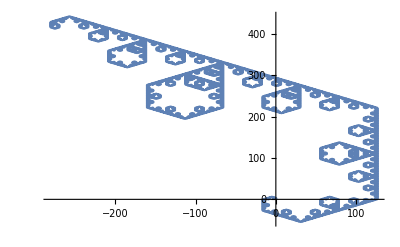
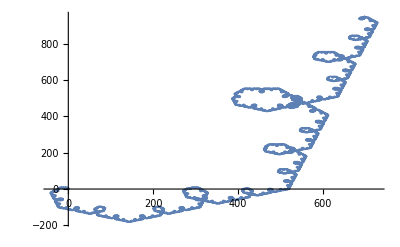
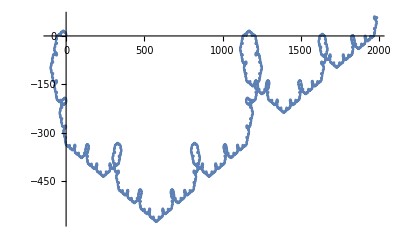
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
(*Table of sumWalks for base 3*)
Sort[Table[{x, ListLinePlot[ReIm /@ expSumList[10000, 3, x]]}, {x, Range[10]}]]
```

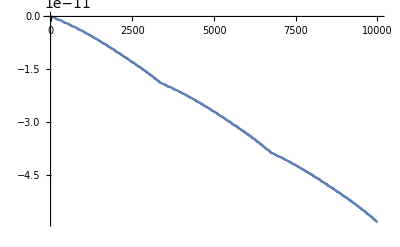
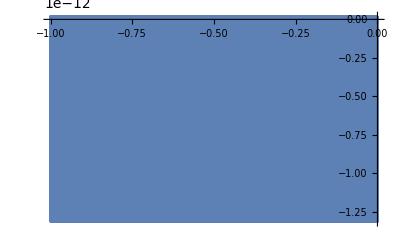
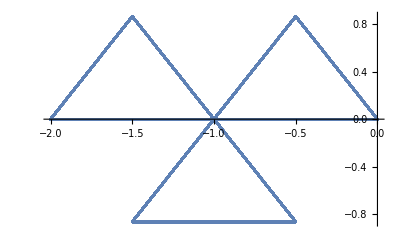
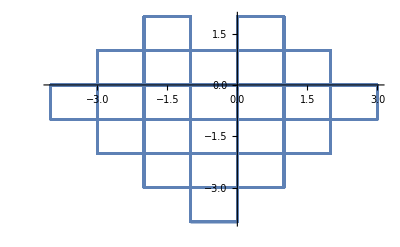
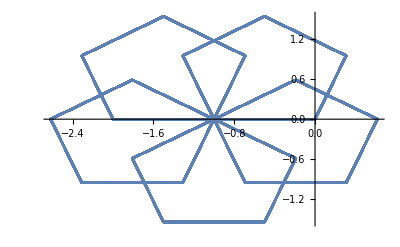
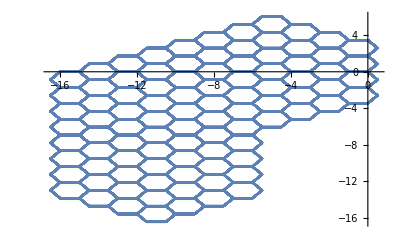
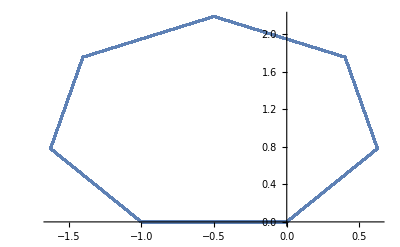
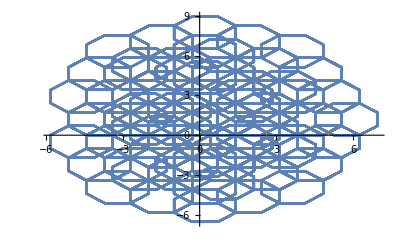
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
(*Table of sumWalks for base 15*)
Sort[Table[{x, ListLinePlot[ReIm /@ expSumList[10000, 15, x]]}, {x, Range[10]}]]
```

```mathematica
Animate[list = ReIm  /@ expSumList[n, b, p];
ListLinePlot[list], {n, 1, 10000, 1}, {b, 2, 15, 1},{p, 2, 15, 1}, AnimationRunning->False]
```

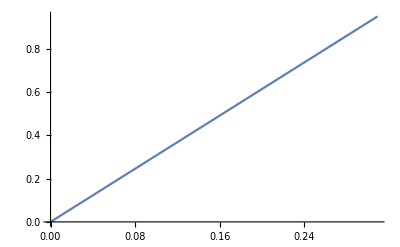
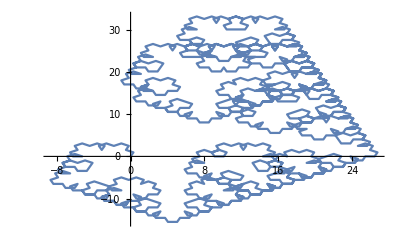
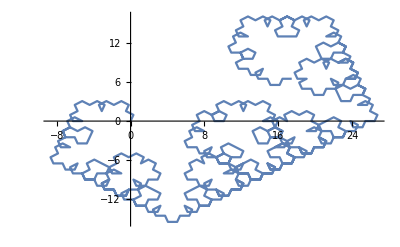
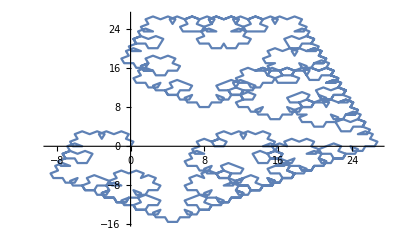
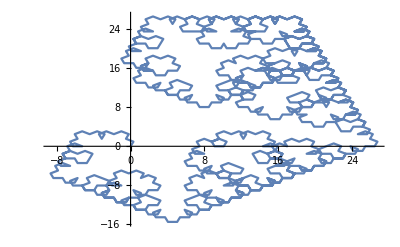
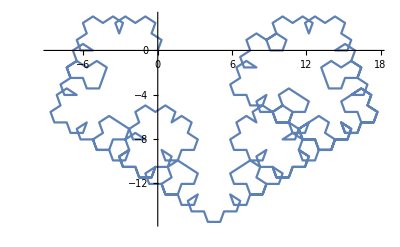
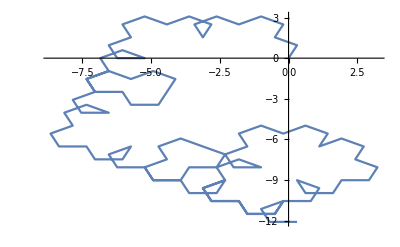
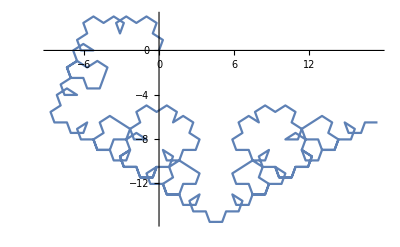
{{1,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{7,-Graphics-},{9,-Graphics-},{11,-Graphics-}}

```mathematica
Sort[Table[{Total[IntegerDigits[x, 3]], ListLinePlot[ReIm /@ expSumList[x, 3, 5]]}, {x, 1, 1001, 100}]]
```

```mathematica
termList=ReIm /@ expSumList[15, 2, 5]
```

{{0,0},{0.309017,0.951057},{0.618034,1.90211},{-0.190983,2.4899},{0.118034,3.44095},{-0.690983,4.02874},{-1.5,4.61653},{-2.30902,4.02874},{-2.,4.9798},{-2.80902,5.56758},{-3.61803,6.15537},{-4.42705,5.56758},{-5.23607,6.15537},{-6.04508,5.56758},{-6.8541,4.9798},{-6.54508,4.02874}}

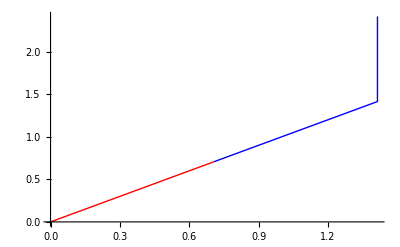
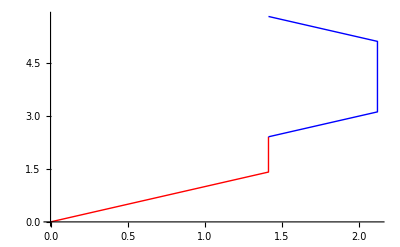
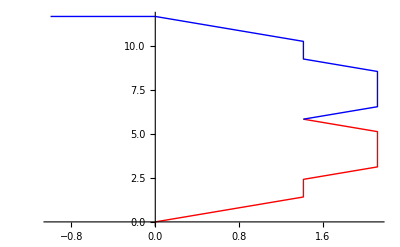
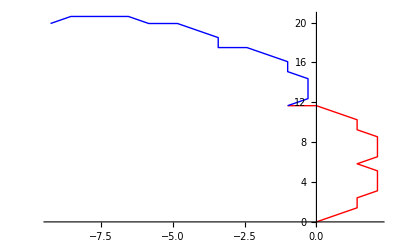
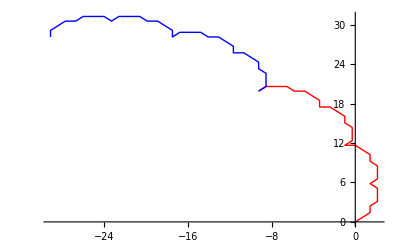
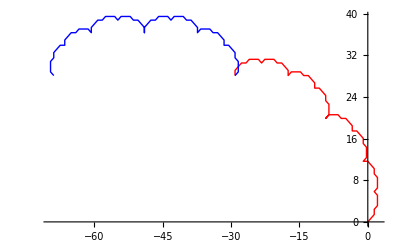
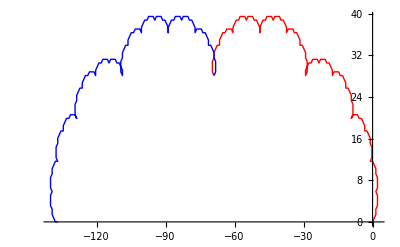
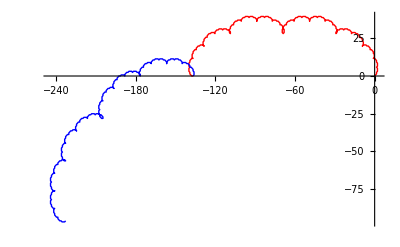

```mathematica
(* chunkVisualizer[1, 2^(k-1), 2, 10, Hue[k/10]], {k,1, 10, 1 } *)
Table[Show[{chunkVisualizer[1, 2^k - 1, 2, 8, Red], chunkVisualizer[2^k, 2^(k+1)-1, 2, 8, Blue]}, PlotRange->Full], {k,1, 15, 1}]
```

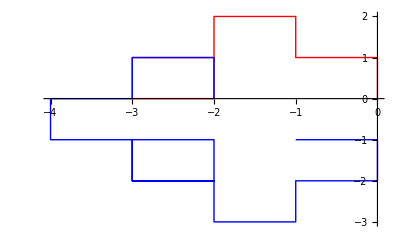

```mathematica
Show[{chunkVisualizer[1, 9, 3, 4, Red], chunkVisualizer[9, 26, 3, 4, Blue]}, PlotRange->Full]
```

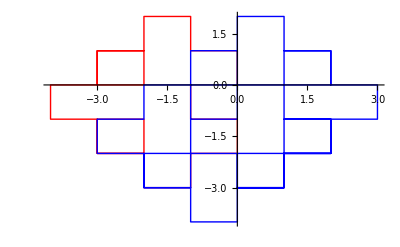

```mathematica
Show[{chunkVisualizer[1, 27, 3, 4, Red], chunkVisualizer[27, 81, 3, 4, Blue]}, PlotRange->Full]
```

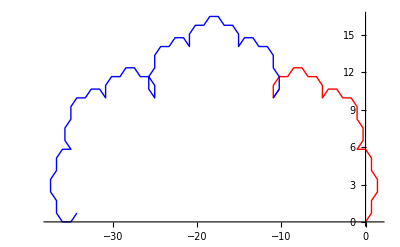

```mathematica
Show[{chunkVisualizer[1, 27, 3, 8, Red], chunkVisualizer[27, 81, 3, 8, Blue]}, PlotRange->Full]
```

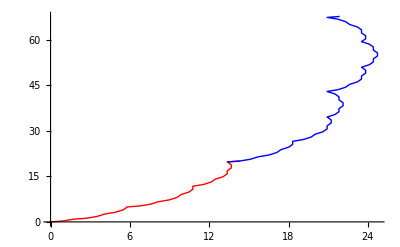

```mathematica
Show[{chunkVisualizer[1, 27, 3, 20, Red], chunkVisualizer[27, 81, 3, 20, Blue]}, PlotRange->Full]
```

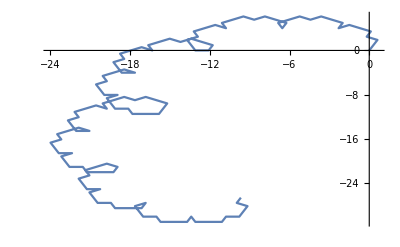
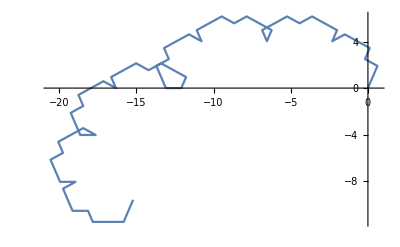
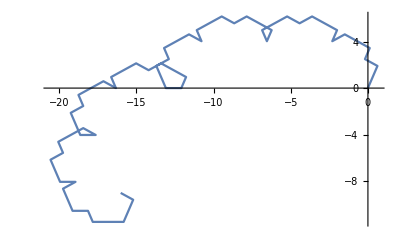
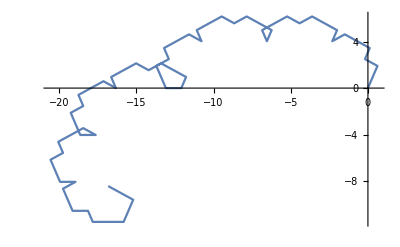
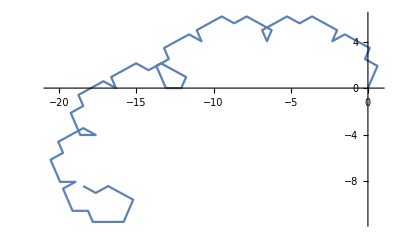
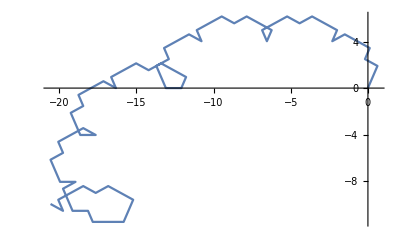
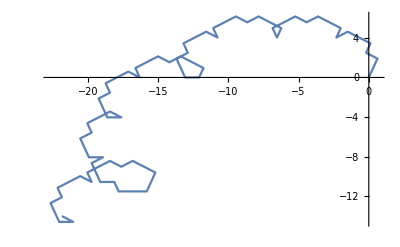
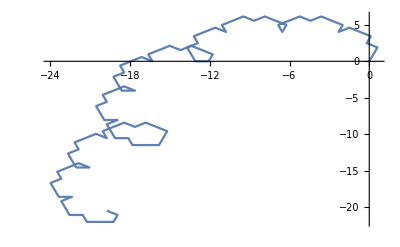
{{1,-Graphics-},{1,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{7,-Graphics-}}

```mathematica
Sort[Table[{Total[IntegerDigits[x, 2]], ListLinePlot[ReIm /@ expSumList[x, 2, 5]]}, {x, 64, 128, 1}]]
```

```mathematica
expSumList[5, 2, 7]
```

{0,0.62349+0.781831 ⅈ,1.24698+1.56366 ⅈ,1.02446+2.53859 ⅈ,1.64795+3.32042 ⅈ,1.42543+4.29535 ⅈ}

```mathematica
arrowVisualizer[n_, b_, p_]:=Graphics[
{Cyan,
Thickness[0.0075],
Arrowheads[0.1], 
Arrow[ReIm /@ expSumList[#,b, p]]&/@ Range[n]}, 
AspectRatio->1, 
Background->Black
]
```

```mathematica
arrowVisualizer[5,2,7]
```

-Graphics-

```mathematica
Show[{visualizer[100,10,Pi]}, LabelStyle->Large, Axes->False]
```

-Graphics-

```mathematica
Show[{pointVisualizer[50, 7, 6], visualizer[50,7,6]}, LabelStyle->Large]
```

-Graphics-

```mathematica
(*Cases where b = p*)
Table[Show[{chunkVisualizer[1, 2^k - 1, 4, 4, Red], chunkVisualizer[2^k, 2^(k+1)-1, 4, 4, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 3, 3, Red], chunkVisualizer[2^k, 2^(k+1)-1, 3, 3, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 5, 5, Red], chunkVisualizer[2^k, 2^(k+1)-1, 5, 5, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 6, 6, Red], chunkVisualizer[2^k, 2^(k+1)-1, 6, 6, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Cases where b = 1 mod p*)
Table[Show[{chunkVisualizer[1, 2^k - 1, 4, 3, Red], chunkVisualizer[2^k, 2^(k+1)-1, 4, 3, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 5, 4, Red], chunkVisualizer[2^k, 2^(k+1)-1, 5, 4, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 6, 5, Red], chunkVisualizer[2^k, 2^(k+1)-1, 6, 5, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 7, 6, Red], chunkVisualizer[2^k, 2^(k+1)-1, 7, 6, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Table of all the b = p cases up to 10*)
Table[{n, Show[{chunkVisualizer[1, 2^(k)-1, n, n, Blue]}, PlotRange->Full]}, {n,5, 25, 5}, {k, 10, 15, 1}]
```

{{{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-}},{{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-}},{{15,-Graphics-},{15,-Graphics-},{15,-Graphics-},{15,-Graphics-},{15,-Graphics-},{15,-Graphics-}},{{20,-Graphics-},{20,-Graphics-},{20,-Graphics-},{20,-Graphics-},{20,-Graphics-},{20,-Graphics-}},{{25,-Graphics-},{25,-Graphics-},{25,-Graphics-},{25,-Graphics-},{25,-Graphics-},{25,-Graphics-}}}

```mathematica
(*Irrational p values*)
Table[Show[{chunkVisualizer[1, 2^(8), n, Pi, Blue]}, PlotRange->Full], {n,{2, 3, 9, 10}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^(8+1)-1, n, GoldenRatio, Blue]}, PlotRange->Full], {n,{2, 3, 9, 10}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^(8+1)-1, n, EulerGamma, Blue]}, PlotRange->Full], {n,{2, 3, 9, 10}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^(8+1)-1, n, Sqrt[2], Blue]}, PlotRange->Full], {n,{2, 3, 9, 10}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Koch Curve graphing*)
twistExpSumList[n_, b_, p_, q_] := Prepend[Accumulate[(Exp[2.0*Pi*I*(sumIntDigits[#, b]/p + (#/q))]&/@Range[n])], 0]
twistVisualizer[n_, b_, p_, q_]:=ListLinePlot[ReIm /@ twistExpSumList[n,b, p, q], PlotStyle->Thick]
```

```mathematica
twistVisualizer[1000, 2, 2, 3]
```

-Graphics-